# Blatt 5 - Optimierung der Emittanz im DBA-Lattice

Jonas Neundorf & Jan Skottke

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

## Berechnung der Dispersionfunktion

Definiere die Matritzen für die Magnete:

```mathematica
mF[f_]:={{1,0,0},{-1/f,1,0},{0,0,1}} (*fokussierender Quad*)
```

```mathematica
mD[s_, ρ_] := {{Cos[s/ρ], ρ*Sin[s/ρ], ρ*(1 - Cos[s/ρ])}, {-1/ρ*Sin[s/ρ], Cos[s/ρ], Sin[s/ρ]}, {0, 0, 1}}(*Dipol*)
```

Definiere Dispersionsfunktionen:

```mathematica
η[s_]:=ρ*(1-Cos[s/ρ])
```

```mathematica
dη[s_]=D[η[s],s];
```

Bestimmte f:

```mathematica
eq={0,0,1}==mD[s,ρ].mF[f].mD[s,ρ].{η[0],dη[0],1}//FullSimplify (*Dispersion nach dem ersten Dipol*)
```

{0,0,1}=={(ρ (2 f-2 f Cos[(2 s)/ρ]-2 ρ Sin[s/ρ]+ρ Sin[(2 s)/ρ]))/(2 f),(Cos[s/ρ] (ρ (-1+Cos[s/ρ])+2 f Sin[s/ρ]))/f,1}

```mathematica
focus=Solve[eq,f]
```

{{f→1/2 ρ Tan[s/(2 ρ)]}}

Diese Brennweite muss der Quadropol haben, damit die Dispersion am Ende wieder bei {0,0,1} ist.

#### Tests

Die berechnete Brennweite liefert das gewünschte Ergebnis, dass die Dispersion nach dem 2. Dipol wieder bei {0,0,1} ist.

```mathematica
mD[s,ρ].mF[f].mD[s,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{{0,0,1}}

Dispersion nach dem ersten Dipol:

```mathematica
mD[s,ρ].{η[0],dη[0],1}//FullSimplify
```

{ρ-ρ Cos[s/ρ],Sin[s/ρ],1}

Dispersion nach dem Quadropol und dem zweiten Dipol: (Hier gehen wir nur davon aus, dass der Startpunkt im Quadropol liegt und NICHT im 1. Dipol, da die Dispersion nach dem Quadropol und 2. Dipol ja {η,-dη} sein sollte. Und das ist sie!! :))

```mathematica
mF[f].mD[s,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{{ρ-ρ Cos[s/ρ],-Sin[s/ρ],1}}

KOMMENTAR: Ab hier wollte ich eigentlich einen piecewise plot machen, damit man sieht wie die Dispersion verläuft (wie auf dem Blatt gefordert), aber leider bin ich zu blöd dafür T_T

```mathematica
dispersion[s_]={{{1,0,0},{0,1,0},{0,0,1}},mD[s,ρ].mF[f],mD[L,ρ].mF[f].mD[s,ρ]}.{η[0],dη[0],1}//.focus//FullSimplify
```

{{{0,0,1},{ρ-ρ Cos[s/ρ],Sin[s/ρ],1},{ρ-ρ Cos[(L-s)/ρ],Sin[(L-s)/ρ],1}}}

```mathematica
dispersion[s][[1,1,1]]
```

0

```mathematica
fulldispersion[s_]=Piecewise[{{dispersion[s][[1,1,1]]
dispersion[s][[1,2,1]], s=0
s<=L}, {dispersion[s-L][[1,3,1]], L<s≤2*L}}]
```

Piecewise[{{0, 0}, {ρ-ρ Cos[(2 L)/ρ], L<0≤2 L}, {0, True}}]

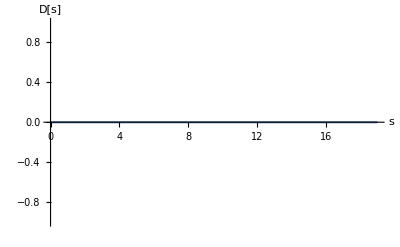

```mathematica
Plot[fulldispersion[x]//.focus//.{L ->5, ρ-> 10000}, {x, 0, 19}, AxesLabel-> {"s", "D[s]"}]
```

## Berechnung der Twiss Parameter (β-Funktionen)

```mathematica
bmat:={{β,-α},{-α,γ}}
```